## Solar Flares & CMEs Problem Set 2 Roy Smart

```mathematica
Clear["Global`*"]
```

## Problem 2

### From 1 to 1.01 solar radii we use the VAL model used by Hurford and Gary 2004

#### Import tabulated data from the VAL model

```mathematica
data=Transpose[Import[FileNameJoin[{NotebookDirectory[],"p2_modelB.csv"}]]];
```

#### Put units in terms of solar radii

```mathematica
h0 = data[[1]] / 695700;
```

#### The number density is the second column

```mathematica
N0 = data[[2]];
```

#### The plasma frequency is given as

```mathematica
νp[n_] := 8980 √n
```

#### Construct a plot of this region

```mathematica
ν0=Transpose[{νp[N0],h0}];
pltrng = {{10^4,5 10^10},{5 10^-4,10^3}};
p0=ListLogLogPlot[ν0,PlotRange->pltrng,Joined->True,ImageSize->Large];
```

### From 1.01 to 1.2 solar radii use model by Mann et al (1997)

#### The functional form given in the paper is

```mathematica
N2 = Ns Exp[A/Rs(1/R-1)] ;
A = (μ G Ms Mp)/(k T);
```

#### with the corresponding values

```mathematica
N2v = {Ns-> Min[N0], μ-> 0.6, G-> 6.674 10^-11,Ms-> 1.988 10^30, k-> 1.38 10^-23,T-> 2 10^6,Rs-> 6.957 10^8,Mp-> 1.672 10^-27};
```

#### Put equation in terms of frequency

```mathematica
R2 = Part[Solve[νp[N2]== ν,R]//Quiet,1,1,2]-1 /. N2v
```

-1+(1.33104×10^-7)/(1.33104×10^-7+1.92013×10^-8 Log[1.49587×10^-17 ν^2])

#### Find min and max frequency

```mathematica
Rmn = Max[h0]+1;
Rmx=2.3;
νmx = νp[N2] /. N2v /. R-> Rmn
νmn= νp[N2] /. N2v /. R-> Rmx
```

2.55252×10^8

3.64545×10^7

#### Construct plot of the region

```mathematica
p2=LogLogPlot[R2 /. N2v,{ν,νmn,νmx},PlotRange->pltrng,ImageSize->Large];
```

### From 1.2-215 solar radii we use the model given by Leblanc et al (1998)

#### The functional form is given as

```mathematica
N4 = α/R^2+β/R^4+γ/R^6;
```

#### The values given in the paper are

```mathematica
N4v={α-> 3.3 10^5,β-> 4.1 10^6,γ-> 8 10^7};
```

#### Put equation in terms of frequency

```mathematica
R4 = Part[Solve[νp[N4]== ν,R] //Quiet,2,1,2];
```

#### Find min and max frequency

```mathematica
Rmn = 1.33;
Rmx=300;
νmx = νp[N4] /. N4v /. R-> Rmn
νmn= νp[N4] /. N4v /. R-> Rmx
```

3.58645×10^7

17196.6

#### Construct plot of the region

```mathematica
p4=LogLogPlot[R4 /. N4v,{ν,νmn,νmx},PlotRange->pltrng,ImageSize->Large];
```

### Construct final plot

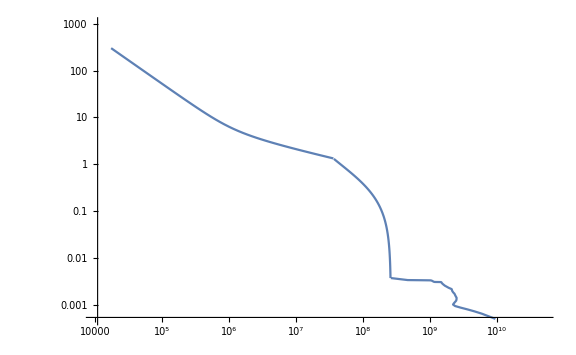

```mathematica
Show[p0,p2,p4]
```

```mathematica
Clear["Global`*"]
```

## Problem 3

### Reproduce frequency drift feature

#### The position of the electron beam is given by the classical velocity, where we take the velocity to be 0.3c

```mathematica
r =(Rs+ 0.3 c tE)/Rs;
```

#### The frequency of the emitted radiation as a function of radius is (in MHz)

```mathematica
fE = 8980 √ne/10^6;
```

#### In the last problem, we found the number density as

```mathematica
ne = α/r^2+β/r^4+γ/r^6/.{α-> 3.3 10^5,β-> 4.1 10^6,γ-> 8 10^7};
```

#### The time the signal arrives at earth is given by

```mathematica
t ==  tE + (RE -Rs r)/c;
```

#### Solve the equation for tE

```mathematica
tE = Part[Solve[t ==  tE + (RE -Rs r)/c ,tE],1,1,2]//FullSimplify
```

(-1.42857 RE+1.42857 Rs+1.42857 c t)/c

#### The pertinent values for this equation are

```mathematica
fEv = {c-> 3 10^10,RE ->  1.5 10^13,Rs-> 6.96 10^10};
```

#### The start time is offset by the light travel time between the earth and the sn

```mathematica
tStart = (RE - Rs)/c /. fEv
```

497.68

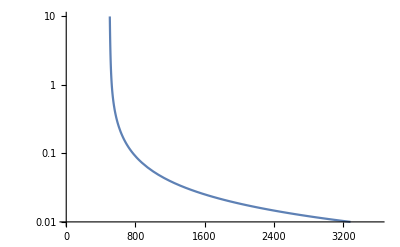

```mathematica
p0 =LogPlot[{fE /. {c-> 3 10^10,RE ->  1.5 10^13,Rs-> 6.96 10^10}},{t,tStart,3600},PlotRange->{{0, 3600},{0.01,10}}]
```

### Reproduce type-III radio burst dynamic spectrum

#### The time-evolution of the peak frequency of type-III radio bursts follows the empirical power law

```mathematica
f = a t^b ;
fv ={a-> 150,b-> -0.6 };
```

#### The FWHM of these bursts is given by the empirical law

```mathematica
Δf = C1 ν;
Δfv = {C1-> 0.57};
```

#### and the empirical frequency-dependent decay is

```mathematica
τD = 10^γ(10^6 ν)^-δ/. ν-> 0.1;
τDv = {γ-> 7.71,δ-> 0.95};
```

#### Plot the dynamic frequency using the curve developed in the first part of the question.

```mathematica
S1=Piecewise[{{Exp[-(4 Log[2](ν - fE)^2)/Δf^2] Exp[-(t-tStart)/τD]/.ν-> 10^ν,t >tStart},{0,t<tStart}}];
p1=DensityPlot[S1/. fv/.Δfv /. τDv /. fEv ,{t,0,3600},{ν,-2,2},ColorFunction->"Rainbow",PlotRange->Full,PlotPoints->100,MaxRecursion->5]
```

-Graphics-

#### Plot the dynamic spectrum using the empirical power law

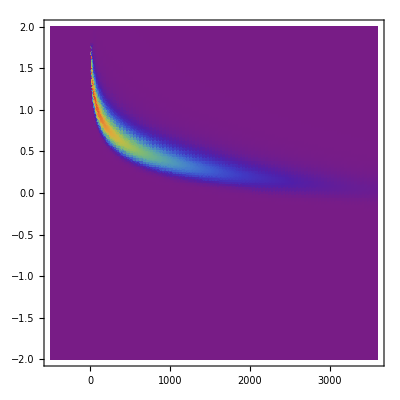

```mathematica
S2=Piecewise[{{Exp[-(4 Log[2](ν - f)^2)/Δf^2] Exp[-(t)/τD]/.ν-> 10^ν,t >0},{0,t<0}}];
p1=DensityPlot[S2/. fv/.Δfv /. τDv /. fEv ,{t,-tStart,3600},{ν,-2,2},ColorFunction->"Rainbow",PlotRange->Full,PlotPoints->100,MaxRecursion->5]
```

#### Comparing to Figure 1 in the Problem Statement, the empirical law and the law derived from the plasma frequency in the heliosphere did not quite match. General shape seems to be correct.

```mathematica
Clear["Global`*"]
```

## Problem 4

### Thermal Bremsstrahlung

#### Gary and Hurford 2004 gives the frequency at which thermal bremsstrahlung reaches optical depth unity as approximately

```mathematica
νtb = 0.5 ne T^(-3/4)L^(1/2);
```

#### Use the scale height also provided in Gary and Hurford (2004)

```mathematica
L = H0 (T/T0)(R/Rs)^2;
H0 = 0.1 Rs;
T0 = 2 10^6;
```

#### Use the hydrostatic equilibrium model for number density given by Mann et al (1997)

```mathematica
N2 = Ns Exp[A/Rs(Rs/R-1)] ;
A = (μ G Ms Mp)/(k T);
N2v = {Ns-> 8.29 10^8, μ-> 0.6, G-> 6.674 10^-8,Ms-> 1.988 10^33, k-> 1.38 10^-16,T-> 2 10^6,Rs-> 6.957 10^10,Mp-> 1.672 10^-24};
```

#### Now we are free to calculate the frequency (in GHz)

```mathematica
(νtb /10^9 /. ne-> N2 /. R -> 1.005 Rs /. T-> T0 /. N2v ) //Framed
```

0.631177

#### Which is approximately where the brightness temperature starts to roll over in Figure 2 in the problem statement.

### Thermal Gyrosychrotron

#### Dulk (1985) gives the optical unity frequency as

```mathematica
N2v =  {Ns->1.21 10^15, μ-> 0.6, G-> 6.674 10^-8,Ms-> 1.988 10^33, k-> 1.38 10^-16,T-> 1 10^8,Rs-> 6.957 10^10,Mp-> 1.672 10^-24};
```

```mathematica
νtg = 475 ((N L)/B)^0.05 Sin[θ]^0.6 T^0.5 B /. θ-> 10 π /180 /. N-> N2
```

71.6876 B T^0.5 ((ⅇ^((G Mp Ms (-1+Rs/R) μ)/(k Rs T)) Ns R^2 T)/(B Rs))^0.05

#### Hurford and Gary (2004) use the magnetic field

```mathematica
B = 0.5 (R/Rs-1)^1.5;
```

#### Evaluate frequency

```mathematica
(νtg /.R-> 1.003 Rs/. N2v) //Framed
```

4685.38

#### This does not look right by many orders of magnitude.